# Project: Random Number Generating Algorithms for Sampling Standard Distributions

## SCIMATH202-Theory of Statistics and Data Analysis Friso Meeusen Last updated: April 20 2023

## Additive Sampling

### Bernoulli Distribution

```mathematica
(* This clears all definitions and variables; Quit Kernel *)
ClearAll[Evaluate[Context[]<>"*"]]
```

```mathematica
(* The number of observations in the Uniform distribution *)
samplesize=10^4;
U=RandomVariate[UniformDistribution[{0,1}],{samplesize}];
```

```mathematica
X=Map[#<p&,U]/.{True->1,False->0};
X
```

{0.694174<p,0.750399<p,9997,0.199026<p}
 |  |  |  |

```mathematica
Manipulate[X=Map[#<p&,U]/.{True->1,False->0};
Histogram[X,{0,2,1/20},"Probability",AxesLabel->{"x","f_X(x)"}],{p,0,1}]
```

Histogram::ldata: U is not a valid dataset or list of datasets.

## Binomial

```mathematica
(* This clears all definitions and variables; Quit Kernel *)
ClearAll[Evaluate[Context[]<>"*"]]
```

```mathematica
(* This defines the sample size (n), the probability for success (p) and the number of times the experiment is repeated (nrepeats) *)
{n=50,p=0.65,nrepeats=10^4};
(* This is just a Table to store the results: *)
BinomDist=Table[,{nrepeats}];
Do[
(* This generates a sample of size n from the Bernoulli distribution: *)
bernsample=RandomInteger[BernoulliDistribution[p],{n}];
(* This takes and stores the sample total:*)
y=Total[bernsample];
BinomDist[[ii]]=y;
,{ii,1,nrepeats}];
```

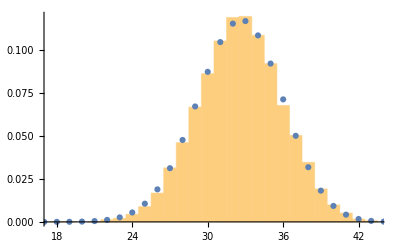

```mathematica
(* The histogram of all obtained sample totals (Binomial distribution): *)
p1=Histogram[BinomDist,{1},"Probability"];
p2=ListPlot[Table[{x,PDF[BinomialDistribution[n,p],x]},{x,0,n}]];
Show[p1,p2]
```

## Geometric

```mathematica
(* This clears all definitions and variables; Quit Kernel *)
ClearAll[Evaluate[Context[]<>"*"]]
```

```mathematica
(* This defines the sample size (n), the probability for success (p) and the number of times the experiment is repeated (nrepeats) *)
{n=50,p=0.65,nrepeats=10^4};
(* This is just a Table to store the results: *)
GeomDist=Table[,{nrepeats}];
```

```mathematica
Do[
(* This generates a sample of size n from the Bernoulli distribution: *)
U=RandomReal[{0,1},n];
bernsample=Map[#<p&,U]/.{True->1,False->0};
(* This defines the first index when the outcome of the Bernoulli trial is 1*)
first1=First[Flatten[Position[bernsample,1,1,1]]];
(* This takes and stores the first index -1 :*)
y=first1-1;
GeomDist[[ii]]=y;
,{ii,1,nrepeats}];
```

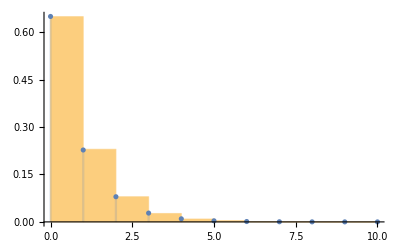

```mathematica
(* The histogram of the obtained geometric distribution on top of the analytical geomeric distribution: *)
p1=Histogram[GeomDist,Automatic,"Probability"];
p2=DiscretePlot[PDF[GeometricDistribution[p],x],{x,0,n}];
Show[p1,p2]
```

## Negative Binomial

```mathematica
(* This clears all definitions and variables; Quit Kernel *)
ClearAll[Evaluate[Context[]<>"*"]]
```

```mathematica
(* This defines the number of successes (r), the probability for success (p) and the number of times the experiment is repeated (nrepeats) *)
{r=50,p=0.65,nrepeats=10^4};
```

```mathematica
(* This is just a Table to store the results: *)
NegBinomDist=Table[,{nrepeats}];
```

```mathematica
Do[
(* This generates a sample of size n from the Bernoulli distribution: *)
bernsample=RandomInteger[GeometricDistribution[p],{r}];
(* This takes and stores the sample total:*)
y=Total[bernsample];
NegBinomDist[[ii]]=y;
,{ii,1,nrepeats}];
```

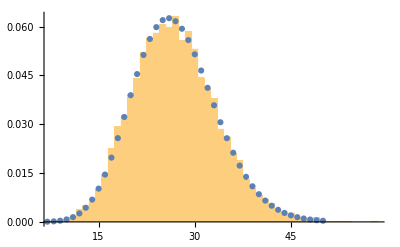

```mathematica
(* The histogram of the obtained Negative Binomial distribution on top of the analytical Negative Binomial distribution: *)
p1=Histogram[NegBinomDist,{1},"Probability"];
p2=ListPlot[Table[{x,PDF[NegativeBinomialDistribution[r,p],x]},{x,0,n}]];
Show[p1,p2]
```

## Hypergeometric

```mathematica
(* This clears all definitions and variables; Quit Kernel *)
ClearAll[Evaluate[Context[]<>"*"]]
```

```mathematica
(* This defines the the total number of items in the population (n1), the sample size (n2) and the number of succes items (k). nrepeats the number of times the experiment is performed. *)
{n1=200,n2=50,k=40,nrepeats=10^5};
(* This is just a Table to store the results: *)
HyperGeomdist=Table[,{nrepeats}];
```

```mathematica
Do[
(* This generates a sample of size n from the Bernoulli distribution: *)
bernsample=RandomInteger[BernoulliDistribution[k/n1],{n2}];
(* This takes and stores the sample total:*)
y=Total[bernsample];
HyperGeomdist[[ii]]=y;
,{ii,1,nrepeats}];
```

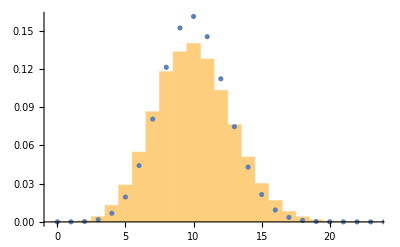

```mathematica
(* The histogram of the obtained Hyper Geometric distribution on top of the analytical Hypergeometric distribution: *)
p1=Histogram[HyperGeomdist,{1},"Probability"];
p2=ListPlot[Table[{x,PDF[HypergeometricDistribution[n2,k,n1],x]},{x,0,100}]];
Show[p1,p2]
```

## Inverse Sampling Methods (ITM)

## Triangular Distribution

```mathematica
(* This clears all definitions and variables; Quit Kernel *)
ClearAll[Evaluate[Context[]<>"*"]]
```

```mathematica
(* this defines the number of observations (n) and the minimum (a), mode (b) and maximum value for the triangular distribution.*)
{n=5*10^4,a=1,b=2,c=3};
```

```mathematica
(* This takes a sample of the uniform distribution: *)
U=RandomReal[{0,1},n];
```

```mathematica
(* This converts the sample of the uniform distribution to a sample of the triangular distribution: *)
f[u_]:=Piecewise[{{√(u(c-a)(b-a))+a,0≤u<(b-a)/(c-a)},{c-√((c-a)(c-b)(1-u)),(b-a)/(c-a)≤u<1}}];
triangular=Map[f[#]&,U];
```

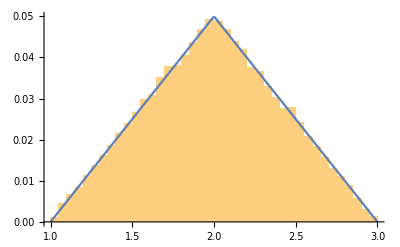

```mathematica
(* This plots the sampled Triangular distribution against the analytical PDF. *)
p1=Histogram[triangular,{a,c,1/5},"Probability",PlotRange->All];
p2=Plot[1/5PDF[TriangularDistribution[{a,c},b],x],{x,a,c},PlotRange->All];
Show[p1,p2]
```

## Exponential Distribution

```mathematica
(* This clears all definitions and variables; Quit Kernel *)
ClearAll[Evaluate[Context[]<>"*"]]
```

```mathematica
(* This defines the number of observations n, and the value for λ *)
```

```mathematica
{n=10^4,λ=3};
```

```mathematica
(* This takes a sample of n observations from the uniform distribution: *)
u=RandomReal[{0,1},n];
```

```mathematica
(* This transforms the sampled uniform distribution into a sample of the Exponential distribution *)
exp=-Log[1-u]/λ;
```

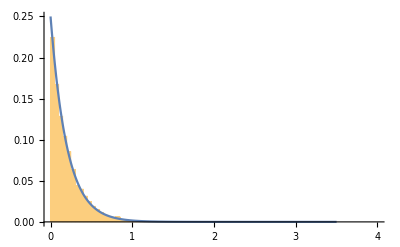

```mathematica
(* This plots the sampled Exponential distribution against the analytical PDF. *)
p1=Histogram[exp,{0,4,1/20},"Probability",PlotRange->All];
p2=Plot[1/20PDF[ExponentialDistribution[λ],x],{x,0,3.5},PlotRange->All];
Show[p1,p2]
```

## Poisson

```mathematica
(* This clears all definitions and variables; Quit Kernel *)
ClearAll[Evaluate[Context[]<>"*"]]
```

```mathematica
(* This defines the value for the rate (λ) and the sample size (n) respectively*)
{n=10^5, λ=7};
```

```mathematica
(* This generates a sample of size n from the unity unfiform distribution: *)
U=RandomReal[{0,1},{n}];
```

```mathematica
(*This transforms U into a sample of the Exponential distribution using the ITM *)
Δt=(-Log[1-U])/λ;
```

```mathematica
(*This transforms the sample from the Exponential distribution into that of a Poisson, by using the method described in the report *)
T=Floor[Accumulate[Δt]];
```

```mathematica
(* Counting the number of Poisson event for each time integer *)
{units,counts}=Transpose[Tally[T]];
```

```mathematica
(*This plots the sampled distribution and the analytical values of the corresponding Poisson distribution *)
p1=Histogram[counts,Automatic,"Probability"];
p2=DiscretePlot[PDF[PoissonDistribution[λ],x],{x,0,14},PlotRange->Full];
```

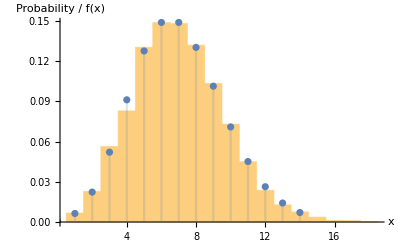

```mathematica
(* This plots the sampled distribution against the analytical values of the corresponding Poisson distribution *)
Show[p1,p2,AxesLabel->{"x","Probability / f(x) "}]
```

## Gamma

```mathematica
(* This clears all definitions and variables; Quit Kernel *)
ClearAll[Evaluate[Context[]<>"*"]]
```

```mathematica
(* This defines, the sample size, the value for λ and the number of times the experiment is repeated respecitvely. *)
{n=25,λ=2,nrepeats=10^4};
(* Empty tables for storing results: *)
yy=Table[,{nrepeats}];
```

```mathematica
Do[
(* This takes a sample of n observations from the uniform distribution: *)
u=RandomReal[{0,1},{n}];
(* This transforms the Uniform distribution into a Exponetial distribution with rate parameter λ. *)
x=(-Log[1-u])/λ;
(* This transforms the Exponetial distribution into a Gamma distribution with shape and rate parameter n,λ*)
y=Total[x];
yy[[ii]]=y;
,{ii,1,nrepeats}];
```

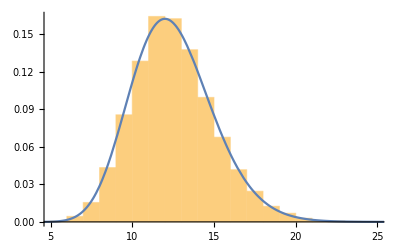

```mathematica
(* This plots the sampled Gamma distribution against the analytical PDF. *)
p1=Histogram[yy,{1},"Probability"];
p2=Plot[PDF[GammaDistribution[n,1/λ],x],{x,0,3 n},PlotRange->All];
Show[p1,p2]
```

## Beta

```mathematica
(* This clears all definitions and variables; Quit Kernel *)
ClearAll[Evaluate[Context[]<>"*"]]
```

```mathematica
(* This defines the shape parameters a and b, and the rate parameter β for the random variables X~Gamma(a,β), Y~Gamma(b,β). Furthermore, the number of iid exponential distributions is defined for generating the X (nexpx) and Y (nexpy)*)
{a=nexpx=2,b=nexpy=3,λ=3,nobs=5*10^4};
```

```mathematica
(* Empty tables for storing results: *)
ww=Table[,{nobs}];
```

```mathematica
Do[
(* This generates two samples of the uniform distributions of length a and b.*)
u1=RandomReal[{0,1},{a}];
u2=RandomReal[{0,1},{b}];
(* This transforms the uniform distributions into the ones of the Exponential distributions with rate parameter λ*)
x=(-Log[1-u1])/λ;
y=(-Log[1-u2])/λ;
(* This transforms the Exponetial distributions into Gamma distributions, where xx~Gamma(a,λ)and yy~Gamma(a,λ)*)
xx=Total[x];
yy=Total[y];
(* This transforms the Gamma distributions into a Beta distribution with parameters (a,b) *)
ww[[ii]]=xx/(xx+yy);
,{ii,1,nobs}];
```

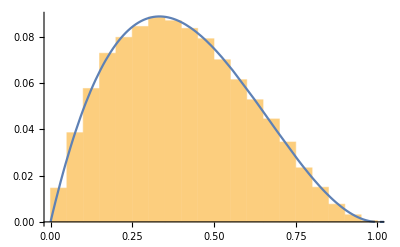

```mathematica
(* This plots the sampled Beta distribution against the analytical PDF. *)
p1=Histogram[ww,{0,1,1/20},"Probability"];
p2=Plot[1/20 PDF[BetaDistribution[a,b],x],{x,0,25},PlotRange->All];
Show[p1,p2]
```

## Chi-Squared

```mathematica
(* This clears all definitions and variables; Quit Kernel *)
ClearAll[Evaluate[Context[]<>"*"]]
```

```mathematica
(* This defines the  degrees of freedom ν and the number of sampled observations n.*)
```

```mathematica
{ν=8,λ=1/2,nrepeats=5*10^4};
```

```mathematica
(* Empty tables for storing results: *)
yy=Table[,{nrepeats}];

(* This generates a sample of the uniform distribution with n observations. 
u=RandomReal[{0,1},n];
Y=RandomVariate[GammaDistribution[ν/2,2],n];*)
```

```mathematica
Do[
u=RandomReal[{0,1},{ν/2}];
x=(-Log[1-u])/λ;
y=Total[x];
yy[[ii]]=y;
,{ii,1,nrepeats}];
```

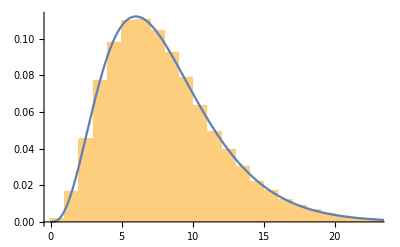

```mathematica
(* This plots the sampled Chi-Squared distribution against the analytical PDF. *)
p1=Histogram[yy,{1},"Probability"];
p2=Plot[PDF[ChiSquareDistribution[ν],x],{x,0,25},PlotRange->All];
Show[p1,p2]
```

## Box-Mueller Transform (BTM)

```mathematica
(* This clears all definitions and variables; Quit Kernel *)
ClearAll[Evaluate[Context[]<>"*"]]
```

```mathematica
(* This generates two  uniform distributions called U1 and U2, with sample size nsize. *)
nsize=10^6;
U1=RandomReal[{0,1},nsize];
U2=RandomReal[{0,1},nsize];
```

```mathematica
(* This defines the Box Mueller transform *)
X=√(-2Log[U1]) Cos[2π U2];
Y=√(-2Log[U1]) Sin[2π U2];
```

```mathematica
(* This shows the sampled standardized normal distribution on top of the analytical normal distribution *)
p1=Histogram[X,{-2,2,1/5},"Probability"];
p2=Plot[1/5 PDF[NormalDistribution[],x],{x,-2,2},PlotRange->All];
```

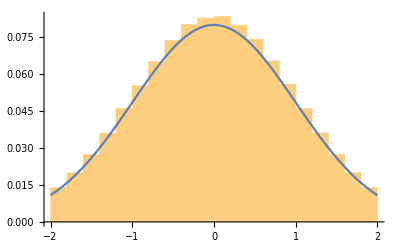

```mathematica
Show[p1,p2]
```

```mathematica
(* This defines the new standard deviation and mean of the non-standardized normal distribution *)
{σ=2,μ=1};
```

```mathematica
(* Z is the random variable which follows the non-standard normal distribution, which is derived by transformation of the variable X. *)
Z=σ X+μ;
```

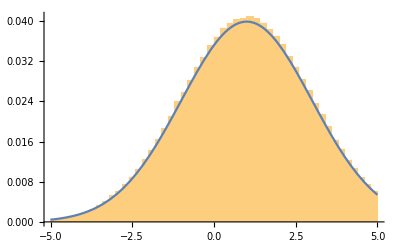

```mathematica
(* This shows the non-normal distribution (that is transformed from the ) on top of the analytical normal distribution *)
p3=Histogram[Z,{-5,5,1/5},"Probability"];
p4=Plot[1/5 PDF[NormalDistribution[μ,σ],x],{x,-5,5},PlotRange->All];
Show[p3,p4]
```

## Accept and Reject Sampling (ARM)

## Geometric

```mathematica
(* This clears all definitions and variables; Quit Kernel *)
ClearAll[Evaluate[Context[]<>"*"]]
```

```mathematica
(* This defines the sample size n and the probabiity for success*)
{n=5*10^4,p=1/3};
```

```mathematica
(*This defines an empty table with intially 0 rows and columns. It will be used to store the results. *)
Geom=Table[u=RandomReal[];
i=0;
While[u>= p, u=RandomReal[{0,1}];
i++];
(*In the While loop a sample of the uniform is generated and it is checked whether or not this sample meets our acceptance criterion: u ≥ p. When this happens, the number of iterations (N), that it took to get to the first sucess is accepted as a sample and is stored in the table. *)
i, 
{n}];
```

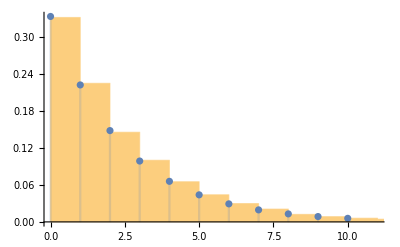

```mathematica
p1=Histogram[Geom,Automatic,"Probability"];
p2=DiscretePlot[PDF[GeometricDistribution[p],x],{x,0,10}];
Show[p1,p2]
```

## Poisson

```mathematica
(* This clears all definitions and variables; Quit Kernel *)
ClearAll[Evaluate[Context[]<>"*"]]
```

```mathematica
(* This defines the sample size n and the rate parameter λ *)
{n=5*10^4,λ=6};
```

```mathematica
(*Recall the definition of the inverse CDF of the Exponential distribution: *)
Expon[u_]=(-Log[1-u])/λ;
```

```mathematica
(*This defines an empty table with intially 0 rows and columns. It will be used to store the results. *)
Poiss=Table[Module[{u}, u=RandomReal[{0,1}];
i=0;
t=Expon[u];
(*The While loop below continues until t ≥ 1. When this condition is no longer met the loop stops, and the resulting observations are accepted and stored in the table.*)
While[t<1, i++;
u=RandomReal[{0,1}];
t+=Expon[u];];
i], {n}];
```

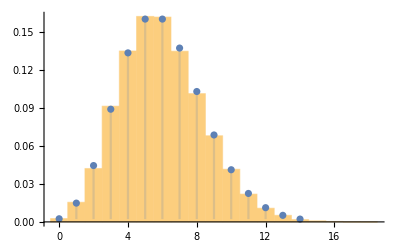

```mathematica
p1=Histogram[Poiss, Automatic,"Probability"];
p2=DiscretePlot[PDF[PoissonDistribution[λ],x],{x,0,14},PlotRange->Full];
Show[p1,p2]
```

## Exponential

```mathematica
(* This clears all definitions and variables; Quit Kernel *)
ClearAll[Evaluate[Context[]<>"*"]]
```

```mathematica
(* This defines the sample size n and the rate parameter λ *)
{n=5*10^4,λ=4};
```

```mathematica
(* This defines and plots the target distribution, f(x) *)
f[x_]=PDF[ExponentialDistribution[λ],x];
```

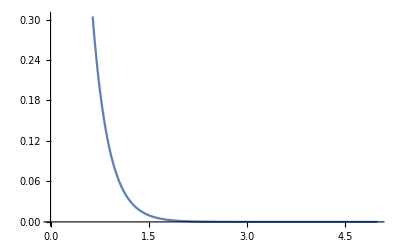

```mathematica
Plot[f[x],{x,0,5}]
```

```mathematica
(* As can be seen in the plot above, the the probability of of obtatining a value for x ≥2 is relatively low, however, even if x increases further the probaility never becomes zero. Lets define the upperbound (up) for the analysis, where up=f[x]==0.001*)
sol=NSolve[f[x]==0.001,x];
up=x/.sol[[1]];
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
(* The proposed distribution now becomes the normalized uniform distribution with the range of (0,up) *)
g[x_]=1/up;
```

```mathematica
(* Now compute the maximum value of this distribution and set this equal to the value for the constant c, to make sure that the proposed distribution completely envelops 
the target distribution. *)
c=First[FindMaximum[f[x]/g[x],x]];
```

```mathematica
(* This is just an empty table of "n" elements to store the results *)
exptab=Table[,{n}];
```

```mathematica
(* This generates samples from the Uniform Distribution with range (0, 1) (u) and an observation from the Uniform Distribution with range (0, 2) (y) (proposed distrbution). Both samples are stored  as a pair in the previously defined table.*)
Do[
unisamples={};
u=RandomReal[{0,1}] ;
y=RandomReal[{0,2}];
pair={u,y};
AppendTo[unisamples,pair];
exptab[[ii]]=unisamples;
,{ii,1,n}]
```

```mathematica
(* This defines the acceptance rejection criterion for this example.  the sample y is accepted when u < f[y]/c*g[y]. *)
accept=Cases[exptab,{{u_,y_}}/; u≤f[y]/(c*g[y]) ];
```

```mathematica
accepted =Flatten[accept,1][[All,2]];
```

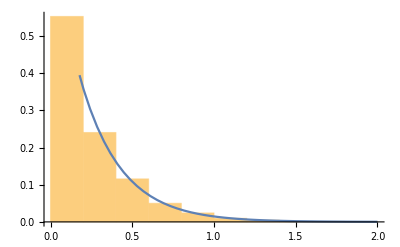

```mathematica
(* This shows the generated sample against the analtical PDF *)
p1=Histogram[accepted,{0,2,1/5},Probability];
p2=Plot[1/5 f[x],{x,0,2}];
Show[p1,p2]
```

## Gamma

```mathematica
(* This clears all definitions and variables; Quit Kernel *)
ClearAll[Evaluate[Context[]<>"*"]]
```

```mathematica
(* This defines the sample size n and the shape α and rate parameter λ respecitvely *)
{n=5*10^4, α=2,λ=3};
```

```mathematica
(* This defines and plots the target distribution, f(x) *)
f[x_]=λ^α/Gamma[α] x^(α-1)Exp[-λ x];
```

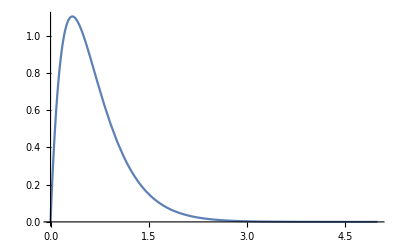

```mathematica
Plot[f[x],{x,0,5}]
```

```mathematica
(* As can be seen in the plot above, the the probability of of obtatining a value for x ≥ 2 is relatively low, however, even if x increases further the probaility never becomes zero. Lets define the upperbound (up) for the analysis where f[x]≤0.001*)
sol=NSolve[f[x]==0.001,x];
up=x/.sol[[2]];
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
(* The proposed distribution now becomes the normalized uniform distribution with the range of (0,up) *)
g[x_]=1/up;
```

```mathematica
(* Now compute the maximum value of this distribution and set this equal to the value for the constant c, to make sure that the proposed distribution completely envelops 
the target distribution. *)
c=First[FindMaximum[f[x]/g[x],x]];
```

```mathematica
(* This is just an empty table of "n" elements to store the results *)
Gammtab=Table[,{n}];
```

```mathematica
(* This generates samples from the Uniform Distribution with range (0, 1) (u) and an observation from the Uniform Distribution with range (0, up) (y). Both samples are stored  as a pair in the previously defined table.*)
Do[
unisamples={};
u=RandomReal[{0,1}] ;
y=RandomReal[{0,up}];
pair={u,y};
AppendTo[unisamples,pair];
Gammtab[[ii]]=unisamples;
,{ii,1,n}]
```

```mathematica
(* This defines the acceptance rejection criterion for this example.  the sample y is accepted when u < f[y]/c*g[y]. *)
accept=Cases[Gammtab,{{u_,y_}}/; u≤f[y]/(c*g[y]) ];
```

```mathematica
accepted =Flatten[accept,1][[All,2]];
```

```mathematica
(* This shows the generated sample against the analtical PDF *)
p1=Histogram[accepted,{0,2,1/20},Probability];
p2=Plot[1/20 f[x],{x,0,5}];
```

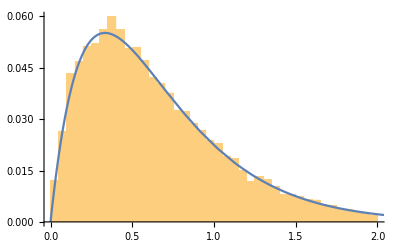

```mathematica
Show[p1,p2]
```

## Beta

```mathematica
(* This clears all definitions and variables; Quit Kernel *)
ClearAll[Evaluate[Context[]<>"*"]]
```

```mathematica
(* This defines the sample size n and the shape α and rate parameter β=λ respecitvely *)
{n=5*10^4, α=2,β=λ=3};
```

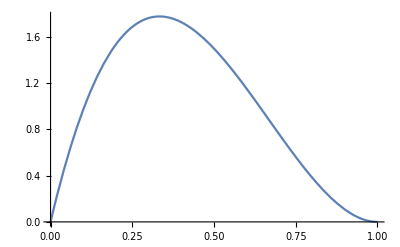

```mathematica
(* This defines and plots the target distribution, f(x) *)
f[x_]=1/Beta[α,β] x^(α-1)(1-x)^(β-1);
Plot[f[x],{x,0,1}]
```

```mathematica
(* The Beta distribution is only defined for defined for 0<x<1. Therefore, the proposed distrbibution is just the normal uniform distribution *) 
g[x_]=1;
```

```mathematica
(* The value for c simply becomes the maximum value of the Beta distribution *)
c=First[FindMaximum[f[x],{x,0,1}]];
```

```mathematica
(* This is just an empty table of "n" elements to store the results *)
Betatab=Table[,{n}];
```

```mathematica
(* This generates samples from the Uniform Distribution with range (0, 1) (u) and an observation from the Uniform Distribution with range (0, 1) (y). Both samples are stored  as a pair in the previously defined table.*)
Do[
unisamples={};
u=RandomReal[{0,1}] ;
y=RandomReal[{0,1}];
pair={u,y};
AppendTo[unisamples,pair];
Betatab[[ii]]=unisamples;
,{ii,1,n}]
```

```mathematica
(* This defines the acceptance rejection criterion for this example.  the sample y is accepted when u < f[y]/c*g[y]. *)
accept=Cases[Betatab,{{u_,y_}}/; u≤f[y]/(c*g[y]) ];
accepted =Flatten[accept,1][[All,2]];
```

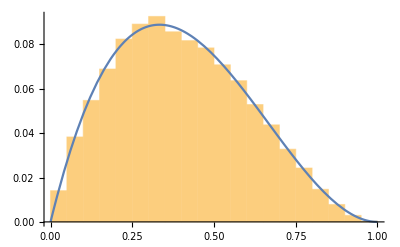

```mathematica
(* This shows the generated sample against the analtical PDF *)
p1=Histogram[accepted,{0,1,1/20},Probability];
p2=Plot[1/20 f[x],{x,0,1}];
Show[p1,p2]
```

## Polynomial

```mathematica
(* This clears all definitions and variables; Quit Kernel *)
ClearAll[Evaluate[Context[]<>"*"]]
```

```mathematica
(* This defines the sample size n ,the power terms: a4-a0, and the upper bound of the distribution. *)
{n=5*10^4,a4=4,a3=-2,a2=-3,a1=1,a0=5,up=7};
```

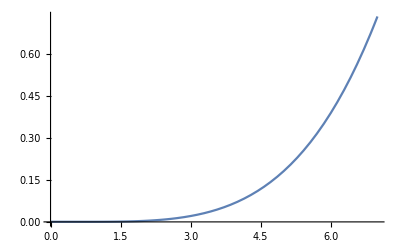

```mathematica
Poly[x_]=a4 x^4+a3 x^3+a2 x^2+a1 x + a0;
A=Integrate[Poly[x],{x,0,up}];
f[x_]=Piecewise[{{Poly[x]/A, 0≤x≤up}, {0, True}}];
Plot[f[x],{x,0,up}]
```

```mathematica
(* The proposed PDF, g(x), is given as the normalized Uniform distribution from 0 to up *)
g[x_]=1/up;
```

```mathematica
(* The value for c is Max[f[x]/g[x]] *)
c=First[FindMaximum[f[x]/g[x],x]];
```

```mathematica
(* This is just an empty table of "n" elements to store the results *)
Polynomtab=Table[,{n}];
```

```mathematica
(* This generates samples from the Uniform Distribution with range (0, 1) (u) and an observation from the Uniform Distribution with range (0, 1) (y). Both samples are stored  as a pair in the previously defined table.*)
Do[
unisamples={};
u=RandomReal[{0,1}] ;
y=RandomReal[{0,up}];
pair={u,y};
AppendTo[unisamples,pair];
Polynomtab[[ii]]=unisamples;
,{ii,1,n}]
```

```mathematica
(* This defines the acceptance rejection criterion for this example.  the sample y is accepted when u < f[y]/c*g[y]. *)
accept=Cases[Polynomtab,{{u_,y_}}/; u≤f[y]/(c*g[y]) ];
accepted =Flatten[accept,1][[All,2]];
```

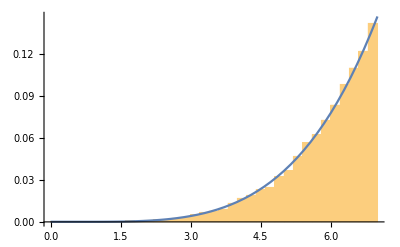

```mathematica
(* This shows the generated sample against the analtical PDF *)
p1=Histogram[accepted,{0,up,1/5},Probability];
p2=Plot[1/5 f[x],{x,0,up}];
Show[p1,p2]
```

## Weibull

```mathematica
(* This clears all definitions and variables; Quit Kernel *)
ClearAll[Evaluate[Context[]<>"*"]]
```

```mathematica
(* This defines the sample size n, and the scale (k), shape (λ), and location (θ) parameter respecitvely. *)
{n=5*10^4,k=2,λ=3,θ=1};
```

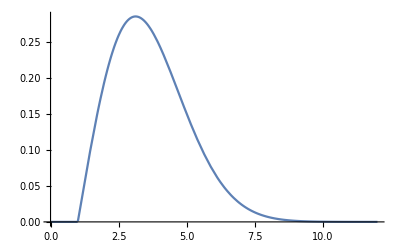

```mathematica
(* This defines and plots the target distribution, f(x) *)
f[x_]=Piecewise[{{k/λ((x-θ)/λ)^(k-1)Exp[-((x-θ)/λ)^k], x≥θ}, {0, x<θ}}];
Plot[f[x],{x,0,12}]
```

```mathematica
(* As can be seen in the plot above, the the probability of of obtatining a value for x ≥ 10 is relatively low, however, even if x increases further the probaility never becomes zero. Lets define the upperbound (up) for the analysis where f[x]≤0.001*)
sol=NSolve[f[x]==0.001,x];
up=x/.sol[[2]];
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
(* The proposed distribution now becomes the normalized uniform distribution with the range of (0,up) *)
g[x_]=1/(up-θ);
```

```mathematica
(* Now compute the maximum value of this distribution and set this equal to the value for the constant c, to make sure that the proposed distribution completely envelops 
the target distribution. *)
c=First[FindMaximum[f[x]/g[x],x]];
```

```mathematica
(* This is just an empty table of "n" elements to store the results *)
Weibulltab=Table[,{n}];
```

```mathematica
(* This generates samples from the Uniform Distribution with range (0, 1) (u) and an observation from the Uniform Distribution with range (0, up) (y). Both samples are stored  as a pair in the previously defined table.*)
Do[
unisamples={};
u=RandomReal[{0,1}] ;
y=RandomReal[{θ,up}];
pair={u,y};
AppendTo[unisamples,pair];
Weibulltab[[ii]]=unisamples;
,{ii,1,n}]
```

```mathematica
(* This defines the acceptance rejection criterion for this example.  the sample y is accepted when u < f[y]/c*g[y]. *)
accept=Cases[Weibulltab,{{u_,y_}}/; u≤f[y]/(c*g[y]) ];
accepted =Flatten[accept,1][[All,2]];
```

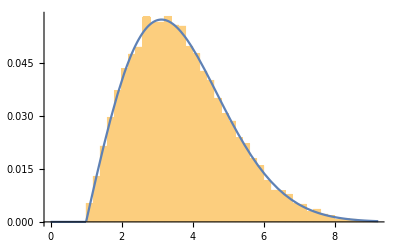

```mathematica
(* This shows the generated sample against the analtical PDF *)
p1=Histogram[accepted,{0,up,1/5},Probability];
p2=Plot[1/5 f[x],{x,0,up}];
Show[p1,p2]
```